# Weyl component erasing

## Definitions

```mathematica
(*Weyl operators*)
Weyl[m_,n_,d_]:=Sum[Exp[(2π I j m)/d]Outer[Times,Normal[SparseArray[{j+1}->{1},{d}]],Normal[SparseArray[{Mod[j+n,d]+1}->{1},{d}]]],{j,0,d-1}]

(*Alejos' Choi matrix definition via tensor products of Weyl operators actind on a d-space*)
ChoiWeyl[τ_List]:=Module[{d},d=Dimensions[τ][[1]];1/d Sum[τ[[μ+1,ν+1]]KroneckerProduct[Weyl[μ,ν,d],Conjugate[Weyl[μ,ν,d]]],{μ,0,d-1},{ν,0,d-1}]]

(*Alejo's expression for eigenvalues of a Weyl operator's Choi matrix*)
λ[τ_,k_,l_]:=Module[{d,ω},
d=Dimensions[τ][[1]];
ω=Exp[2π ⅈ/d];
FullSimplify[1/d Sum[τ[[μ+1,ν+1]]*Power[ω,(k ν-μ l)],{μ,0,d-1},{ν,0,d-1}]]]

(*1's and 0's of τ componennts*)
Taus[d_,k_]:=ArrayReshape[Normal[SparseArray[{1}~Join~#->ConstantArray[1,k],{d^2}]],{d,d}]&/@Subsets[Range[2,d^2],{k-1}]

(*Eigenvalues of all d-level-and-k-invariant-components WCE's Choi matrix*)
ChoiWeylEigvals[d_,k_]:=FullSimplify[Eigenvalues[ChoiWeyl[#]]]&/@Taus[d,k]

(*1's and 0's of τ componennts of all d-level-and-k-invariant-components WCE quantum channels*)
WCEQtmCh1s0s[d_,k_]:=Module[{eigvals,τ},eigvals=ChoiWeylEigvals[d,k];
τ=Taus[d,k];Table[If[Element[eigvals[[i]],Reals],If[AllTrue[eigvals[[i]],#≥0&],τ[[i]],Nothing],Nothing],{i,Length[τ]}]]
```

### Checking definitions work

```mathematica
Flatten[Table[Weyl[i,j,3]//MatrixForm,{i,0,2},{j,0,2}]]
ChoiWeyl[{{1,0,0},{0,1,0},{0,0,1}}]//Eigenvalues
Flatten[Table[λ[{{1,0,0},{0,1,0},{0,0,1}},i,j],{i,0,2},{j,0,2}]]
```

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0),(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0),(1 | 0 | 0
0 | ⅇ^((2 ⅈ π)/3) | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3)),(0 | 1 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | 0 | 0),(0 | 0 | 1
ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | ⅇ^(-(2 ⅈ π)/3) | 0),(1 | 0 | 0
0 | ⅇ^(-(2 ⅈ π)/3) | 0
0 | 0 | ⅇ^((2 ⅈ π)/3)),(0 | 1 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | 0 | 0),(0 | 0 | 1
ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | ⅇ^((2 ⅈ π)/3) | 0)}

{1,1,1,0,0,0,0,0,0}

{1,0,0,0,1,0,0,0,1}

## Definitions usage

### Weyl[m, n, d]

```mathematica
MatrixForm/@Flatten[Table[Weyl[m,n,2],{m,0,1},{n,0,1}],1]
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(1 | 0
0 | -1),(0 | 1
-1 | 0)}

```mathematica
MatrixForm/@Flatten[Table[Weyl[m,n,3],{m,0,2},{n,0,2}],1]
```

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0),(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0),(1 | 0 | 0
0 | ⅇ^((2 ⅈ π)/3) | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3)),(0 | 1 | 0
0 | 0 | ⅇ^((2 ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | 0 | 0),(0 | 0 | 1
ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | ⅇ^(-(2 ⅈ π)/3) | 0),(1 | 0 | 0
0 | ⅇ^(-(2 ⅈ π)/3) | 0
0 | 0 | ⅇ^((2 ⅈ π)/3)),(0 | 1 | 0
0 | 0 | ⅇ^(-(2 ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | 0 | 0),(0 | 0 | 1
ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | ⅇ^((2 ⅈ π)/3) | 0)}

### ChoiWeyl[τ]

Funciona sólo para 1 qudit?

```mathematica
τ=Table[RandomInteger[],9]
```

{0,1,1,0,0,0,1,1,1}

```mathematica
τ=Table[RandomInteger[],81]
ArrayReshape[τ,{3,3,3,3}]
```

{1,0,0,0,1,0,1,1,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,0,1,0,0,0,1,1,0,1,1,0,1,0,0,1,0,1,0,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,0,1,1,0,1,0,0,0,1}

{{{{1,0,0},{0,1,0},{1,1,0}},{{0,1,0},{1,0,1},{0,1,0}},{{1,0,0},{0,0,0},{0,0,0}}},{{{0,1,0},{1,0,1},{1,1,0}},{{1,0,0},{0,1,1},{0,1,1}},{{0,1,0},{0,1,0},{1,0,0}}},{{{1,1,0},{1,1,1},{1,0,0}},{{1,1,1},{1,1,1},{0,0,1}},{{0,1,1},{0,1,0},{0,0,1}}}}

```mathematica
Mod[9,3^2]
```

0

```mathematica
ArrayReshape[τ,{3,3}]
```

{{0,1,1},{0,0,0},{1,1,1}}

```mathematica
Flatten[Table[{i,j},{i,0,2},{j,0,2}],1]
```

{{0,0},{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}}

```mathematica
IntegerDigits[Range[0,8],3,2]
```

{{0,0},{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}}

```mathematica
τ=Table[RandomInteger[],81]
```

{1,1,0,0,1,1,0,0,1,1,1,0,1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,1,1,0,1,0,1,0,0,1,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,0,1,0,1,0}

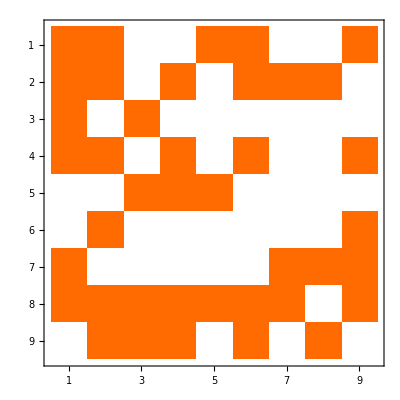

```mathematica
MatrixPlot[ArrayReshape[τ,{9,9}]]
```

```mathematica
ArrayReshape[τ,{3,3,3,3}][[1,1,1,1]]
```

1

```mathematica
ChoiWeyl[ArrayReshape[τ,{3,3}]]//MatrixForm
```

(1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 1/3
0 | 1/3 ⅇ^(-(2 ⅈ π)/3) | 0 | 0 | 0 | 1/3 | 1/3 ⅇ^((2 ⅈ π)/3) | 0 | 0
0 | 0 | 1/3 ⅇ^((2 ⅈ π)/3) | 1/3 | 0 | 0 | 0 | 1/3 ⅇ^(-(2 ⅈ π)/3) | 0
0 | 0 | 1/3 ⅇ^(-(2 ⅈ π)/3) | 1/3 ⅇ^((2 ⅈ π)/3) | 0 | 0 | 0 | 1/3 | 0
1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 1/3
0 | 1/3 ⅇ^((2 ⅈ π)/3) | 0 | 0 | 0 | 1/3 ⅇ^(-(2 ⅈ π)/3) | 1/3 | 0 | 0
0 | 1/3 | 0 | 0 | 0 | 1/3 ⅇ^((2 ⅈ π)/3) | 1/3 ⅇ^(-(2 ⅈ π)/3) | 0 | 0
0 | 0 | 1/3 | 1/3 ⅇ^(-(2 ⅈ π)/3) | 0 | 0 | 0 | 1/3 ⅇ^((2 ⅈ π)/3) | 0
1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 1/3)

```mathematica
IntegerDigits[Range[0,3^6-1],3,6]//Length
```

729

```mathematica
ConstantArray[3,2]
```

{3,3}

```mathematica
lambda[τInput_,d_]:=Module[{ω=Exp[(2π ⅈ)/d],τ=ArrayReshape[τInput,ConstantArray[d,2]]},
Flatten[
Table[
1/d*FullSimplify[Sum[τ[[μ+1,ν+1]]*ω^(k *ν-μ*l),{μ,0,d-1},{ν,0,d-1}]]
,{k,0,d-1},{l,0,d-1}]]
]
```

```mathematica
lambda[{1,0,0,0,0,0,0,0,0},3]
```

{1/3,1/3,1/3,1/3,1/3,1/3,1/3,1/3,1/3}

## Una mejor definición (?)

## d=3

```mathematica
WCEQtmCh3d1To4C=Flatten[WCEQtmCh1s0s[3,#]&/@Range[1,4],1]
```

{{{1,0,0},{0,0,0},{0,0,0}},{{1,1,1},{0,0,0},{0,0,0}},{{1,0,0},{1,0,0},{1,0,0}},{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}}}

```mathematica
WCEQtmCh3d5To9C=Flatten[WCEQtmCh1s0s[3,#]&/@Range[5,9],1]
```

{{{1,1,1},{1,1,1},{1,1,1}}}

```mathematica
WCEQtmCh3d=Join[WCEQtmCh3d1To4C,WCEQtmCh3d5To9C]
GraphicsGrid@ArrayReshape[ArrayPlot[#,ImageSize->80]&/@WCEQtmCh3d,{1,6}]
```

{{{1,0,0},{0,0,0},{0,0,0}},{{1,1,1},{0,0,0},{0,0,0}},{{1,0,0},{1,0,0},{1,0,0}},{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,1,1},{1,1,1},{1,1,1}}}

-Graphics-

```mathematica
{1,1,0,0}
```

```mathematica
AllChoiEigvlsNonNegativeRealsQ[ArrayReshape[KroneckerProduct[{{1,1,1},{0,0,0},{0,0,0}},{1,1,0,0}],{6,6}]]
```

True

### Other definition

```mathematica
AllChoiEigvlsNonNegativeRealsQwλ[τ_]:=Module[{d},d=Length[τ];AllTrue[Flatten[Table[λ[τ,i,j],{i,0,d-1},{j,0,d-1}]],Element[#,NonNegativeReals]&]]
WCEQtmCh1s0sWEigsExp[τ_]:=If[AllChoiEigvlsNonNegativeRealsQwλ[τ]==True,τ,Nothing]
WCEQtmCh1s0sWEigsExp[#]&/@Taus[3,9]
```

{{{1,1,1},{1,1,1},{1,1,1}}}

```mathematica
AbsoluteTiming[ArrayPlot[#,ImageSize->80]&/@Flatten[Table[WCEQtmCh1s0s[3,i],{i,9}],1]]
AbsoluteTiming[ArrayPlot[#,ImageSize->80]&/@Flatten[Table[WCEQtmCh1s0sWEigsExp[#]&/@Taus[3,i],{i,9}],1]]
```

{4.59841,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

{0.355046,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
x={{{1,0,0},{0,0,0},{0,0,0}},{{1,1,1},{0,0,0},{0,0,0}},{{1,0,0},{1,0,0},{1,0,0}},{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,0,1},{0,1,0}},{{1,1,1},{1,1,1},{1,1,1}}};
x={Taus[3,2][[4]]};
Flatten[Table[λ[#,i,j],{i,0,3-1},{j,0,3-1}]]&/@x
FullSimplify[Eigenvalues[ChoiWeyl[#]]]&/@x
```

{{2/3,1/3 (1-(-1)^(1/3)),1/3 (1+(-1)^(2/3)),1/3 (1+(-1)^(2/3)),2/3,1/3 (1-(-1)^(1/3)),1/3 (1-(-1)^(1/3)),1/3 (1+(-1)^(2/3)),2/3}}

{{2/3,2/3,2/3,-1/3 (-1)^(2/3),-1/3 (-1)^(2/3),-1/3 (-1)^(2/3),1/3 (-1)^(1/3),1/3 (-1)^(1/3),1/3 (-1)^(1/3)}}

## d=4

### 2 components invariant

```mathematica
WCEQtmCh1s0s[4,2]
```

{{{1,0,1,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,0,0,0},{1,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}}}

### 4 components invariant

```mathematica
WCEQtmCh4d4C=WCEQtmCh1s0s[4,4]
PCEFigures[Flatten[#]]&/@WCEQtmCh4d4C
```

{{{1,1,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,1,0},{0,0,0,0},{1,0,1,0},{0,0,0,0}},{{1,0,1,0},{0,0,0,0},{0,1,0,1},{0,0,0,0}},{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Checking with Tomás’ results

```mathematica
τ={{1,1,1,1},{1,1,1,1},{0,0,0,0},{0,0,0,0}};ArrayPlot[τ,ImageSize->80]
```

-Graphics-

```mathematica
(*Choi matrix's eigenvalues*)
```

```mathematica
Table[λ[τ,i,j],{i,0,3},{j,0,3}]
```

{{2,1-ⅈ,0,1+ⅈ},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### 5 components invariant

```mathematica
WCEQtmCh4d4C=WCEQtmCh1s0s[4,5]
PCEFigures[Flatten[#]]&/@WCEQtmCh4d4C
```

{}

{}

### All remaining:

```mathematica
WCEQtmCh4d1To3C=Flatten[WCEQtmCh1s0s[4,#]&/@Range[1,3],1];
PCEFigures[Flatten[#]]&/@WCEQtmCh4d1To3C
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Esta vaina se tardó unos minutos, así que mejor copiar el resultado*)
WCEQtmCh4d6To16C=Flatten[WCEQtmCh1s0s[4,#]&/@Range[6,16],1]
```

{{{1,1,1,1},{0,0,0,0},{1,1,1,1},{0,0,0,0}},{{1,0,1,0},{1,0,1,0},{1,0,1,0},{1,0,1,0}},{{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}}

### Summary of results

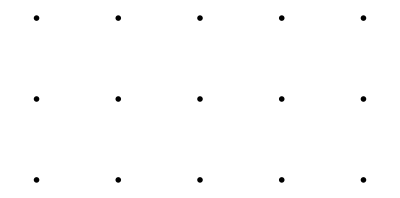

```mathematica
WCEQtmCh4d=Join[WCEQtmCh4d1To3C,WCEQtmCh4d4C,WCEQtmCh4d6To16C];
GraphicsGrid@ArrayReshape[PCEFigures[Flatten[#]]&/@WCEQtmCh4d,{3,5}]
```

### Other definition

```mathematica
AbsoluteTiming[ArrayPlot[#,ImageSize->80]&/@Flatten[Table[WCEQtmCh1s0sWEigsExp[#]&/@Taus[4,i],{i,16}],1]]
```

{27.387,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

## d=5

```mathematica
WCEQtmCh5d5C=WCEQtmCh1s0s[5,5]
```

{{{1,1,1,1,1},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{{1,0,0,0,0},{0,0,1,0,0},{0,0,0,0,1},{0,1,0,0,0},{0,0,0,1,0}},{{1,0,0,0,0},{0,0,0,1,0},{0,1,0,0,0},{0,0,0,0,1},{0,0,1,0,0}},{{1,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,1,0,0},{0,1,0,0,0}}}

```mathematica
ArrayPlot[#,ImageSize->80]&/@WCEQtmCh5d5C
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AbsoluteTiming[ArrayPlot[#,ImageSize->80]&/@(WCEQtmCh1s0sWEigsExp[#]&/@Taus[5,5])]
```

{36.6814,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
AbsoluteTiming[ArrayPlot[#,ImageSize->80]&/@(WCEQtmCh1s0sWEigsExp[#]&/@Taus[5,2])]
```

{0.087242,{}}

```mathematica
x=WCEQtmCh1s0sWEigsExp[#]&/@Taus[5,5]
CheckOPlus[#]&/@x
```

{{{1,1,1,1,1},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0}},{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{{1,0,0,0,0},{0,0,1,0,0},{0,0,0,0,1},{0,1,0,0,0},{0,0,0,1,0}},{{1,0,0,0,0},{0,0,0,1,0},{0,1,0,0,0},{0,0,0,0,1},{0,0,1,0,0}},{{1,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,1,0,0},{0,1,0,0,0}}}

{True,True,True,True,True,True}

```mathematica
Binomial[35,3]
```

6545

```mathematica
RandomInteger[{1,16},5]
```

{8,1,12,12,7}

```mathematica
2^(24)
```

16777216

## Miscellaneous stuff

```mathematica
(*Checking the intersection between 4-level systems Weyl operators and Pauli⊗Pauli*)
weyl4=Flatten[Table[Weyl[i,j,4],{i,0,3},{j,0,3}],1];pauli4=Flatten[Table[Pauli[{i,j}],{i,0,3},{j,0,3}],1];
MatrixForm/@Intersection[weyl4,pauli4]
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

The intersection are 3 non-trivial operators plus the identity.

```mathematica
Length[Subsets[Range[2,16],{#}]]&/@Range[15]
```

{15,105,455,1365,3003,5005,6435,6435,5005,3003,1365,455,105,15,1}

## Random WCE

### Definitions

```mathematica
RandomTauArray[d_]:=ReplacePart[RandomInteger[1,{d,d}],{1,1}->1]
ChoiEigenvalues[τ_]:=Module[{d},
d=Length[τ];
Table[λ[τ,i,j],{i,0,d-1},{j,0,d-1}]
];
AllChoiEigvlsNonNegativeRealsQ[λ_]:=AllTrue[Element[#,NonNegativeReals]&/@Level[λ,{2}],TrueQ]
```

### wer

```mathematica
WCEQtmChannelsTauArrays={};
SeedRandom[132479]
AbsoluteTiming[
Do[τ=RandomTauArray[6];If[AllChoiEigvlsNonNegativeRealsQ[ChoiEigenvalues[τ]]==True,AppendTo[WCEQtmChannelsTauArrays,τ],Nothing],10^4];]
WCEQtmChannelsTauArrays
```

{187.402,Null}

{}

```mathematica
Table[Table[Table[RandomInteger[],3],3],3]
```

{{{0,0,0},{0,0,1},{0,1,1}},{{1,0,0},{0,0,0},{1,1,0}},{{1,0,1},{0,0,1},{1,0,1}}}

## d=6

```mathematica
(*WCEQtmChsd6k2=WCEQtmCh1s0s[6,2];*)
ArrayPlot[#,ImageSize->80]&/@WCEQtmChsd6k2
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
WCEQtmChsd6k3=WCEQtmCh1s0s[6,3];
ArrayPlot[#,ImageSize->80]&/@WCEQtmChsd6k3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WCEQtmChsd6k4=WCEQtmCh1s0s[6,4];
ArrayPlot[#,ImageSize->80]&/@WCEQtmChsd6k4
```

{-Graphics-}

```mathematica
Binomial[35,5]
```

324632

```mathematica
τ={{1,0,0,1,0,0},{0,0,0,0,0,0},{0,0,1,0,0,1},{1,0,0,1,0,0},{0,0,0,0,0,0},{0,0,1,0,0,1}};
ArrayPlot[τ,ImageSize->80]
CheckOPlus[Flatten[τ]]
AbsoluteTiming[Sort@Eigenvalues[ChoiWeyl[τ]]]
AbsoluteTiming[Sort@Eigenvalues[N[ChoiWeyl[τ]]]]
Sort@Flatten@Table[λ[τ,i,j],{i,0,5},{j,0,5}]//FullSimplify
```

-Graphics-

False

{0.080476,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2/3 (-1)^(1/3),2/3 (-1)^(1/3),2/3 (-1)^(1/3),-2/3 (-1)^(2/3),-2/3 (-1)^(2/3),-2/3 (-1)^(2/3),-4/3 (-1)^(1/3) (-1+(-1)^(1/3)),-4/3 (-1)^(1/3) (-1+(-1)^(1/3)),-4/3 (-1)^(1/3) (-1+(-1)^(1/3))}}

{0.042455,{-9.3598×10^-17+3.09377×10^-17 ⅈ,-6.28358×10^-17+7.94745×10^-17 ⅈ,-5.4162×10^-17-8.38979×10^-17 ⅈ,-4.0459×10^-17+2.54358×10^-17 ⅈ,-3.6291×10^-17-4.19489×10^-17 ⅈ,-1.45217×10^-17+2.32949×10^-18 ⅈ,-1.04303×10^-17+1.2178×10^-17 ⅈ,-4.49063×10^-33+4.92427×10^-33 ⅈ,-1.09351×10^-33+1.42509×10^-33 ⅈ,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.46979×10^-18-7.58283×10^-17 ⅈ,9.02247×10^-18-4.52864×10^-17 ⅈ,1.02738×10^-17+2.43005×10^-17 ⅈ,3.20127×10^-17-3.10677×10^-17 ⅈ,3.75934×10^-17-5.68408×10^-18 ⅈ,6.72246×10^-17-6.62224×10^-17 ⅈ,9.46857×10^-17-7.79493×10^-17 ⅈ,1.68869×10^-16+1.02131×10^-16 ⅈ,0.333333+0.57735 ⅈ,0.333333-0.57735 ⅈ,0.333333-0.57735 ⅈ,0.333333+0.57735 ⅈ,0.333333-0.57735 ⅈ,0.333333+0.57735 ⅈ,1.33333-3.33067×10^-16 ⅈ,1.33333-1.11022×10^-16 ⅈ,1.33333+2.22045×10^-16 ⅈ}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4/3,4/3,4/3,-2/3 (-1+(-1)^(1/3)),-2/3 (-1+(-1)^(1/3)),-2/3 (-1+(-1)^(1/3)),2/3 (1+(-1)^(2/3)),2/3 (1+(-1)^(2/3)),2/3 (1+(-1)^(2/3))}

```mathematica
τ=Taus[3,3][[4]]
ArrayPlot[τ,ImageSize->80]
CheckOPlus[τ]
Sort@Eigenvalues[ChoiWeyl[τ]]//FullSimplify
Sort@Flatten@Table[λ[τ,i,j],{i,0,5},{j,0,5}]//FullSimplify
```

{{1,1,0},{0,0,1},{0,0,0}}

-Graphics-

True

{0,0,1,ⅈ/(√3),1/6 (3+ⅈ √3),1/6 (3+ⅈ √3),-ⅈ/(√3),1/6 (3-ⅈ √3),1/6 (3-ⅈ √3)}

{0,0,0,0,0,0,0,0,1,1,1,1,-ⅈ/(√3),-ⅈ/(√3),-ⅈ/(√3),-ⅈ/(√3),ⅈ/(√3),ⅈ/(√3),ⅈ/(√3),ⅈ/(√3),1/3 (2-(-1)^(1/3)),1/3 (2-(-1)^(1/3)),1/3 (2-(-1)^(1/3)),1/3 (2-(-1)^(1/3)),1/3 (2-(-1)^(1/3)),1/3 (2-(-1)^(1/3)),1/3 (2-(-1)^(1/3)),1/3 (2-(-1)^(1/3)),1/3 (2+(-1)^(2/3)),1/3 (2+(-1)^(2/3)),1/3 (2+(-1)^(2/3)),1/3 (2+(-1)^(2/3)),1/3 (2+(-1)^(2/3)),1/3 (2+(-1)^(2/3)),1/3 (2+(-1)^(2/3)),1/3 (2+(-1)^(2/3))}

## Trying stuff

```mathematica
RandomSample[Delete[1]@Flatten[Table[{i,j},{i,6},{j,6}],1],5]
```

{{5,5},{5,2},{1,5},{6,6},{6,1}}

```mathematica
RandomOneQuditTau[d_,k_]:=SparseArray[{{1,1}}~Join~RandomSample[Delete[1]@Flatten[Table[{i,j},{i,d},{j,d}],1],k-1]->ConstantArray[1,k],{d,d}]
ArrayPlot[RandomOneQuditTau[6,6],ImageSize->80]
```

-Graphics-

```mathematica
AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,6]],10]]
AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,6]],10^2]]
AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,6]],10^3]]
```

{0.185985,{}}

{1.21798,{}}

{11.3894,{}}

```mathematica
Binomial[35,5]/3//N
10^5
```

108211.

100000

### Random search for WCE quantum channels. d=6, k=6:

#### Total d=6, k=6 WCE maps:

```mathematica
Binomial[35,5]
```

324632

#### Let us sample roughly 1/3 of that:

```mathematica
AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,6]],10^5]]
```

{1146.44,{SparseArray[…],SparseArray[…],SparseArray[…]}}

#### Checking closure by oplus

```mathematica
x={SparseArray[…],SparseArray[…],SparseArray[…]};
ArrayPlot[#,ImageSize->80]&/@x
CheckOPlus[Flatten[Normal[#]]]&/@x
```

{-Graphics-,-Graphics-,-Graphics-}

{True,True,True}

### d=6, k=8

```mathematica
SeedRandom[412308]
AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,8]],10^5]]
```

{1288.63,{}}

```mathematica
SeedRandom[4123508]
AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,8]],1.8 10^6]]
```

{21653.3,{}}

### d=6, k=12

```mathematica
SeedRandom[2309401]
AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,12]],10^6]]
```

{13226.2,{}}

```mathematica
Binomial[35,11]
```

417225900

```mathematica
WCEQtmCh1s0sWEigsExp[{{1,1,1,1,1,1},{1,1,1,1,1,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]
```

Nothing

Did not found any quantum channel. 
- d=6, k=8: explored around 1/4 of the whole sample of all WCE maps
- d=6, k=12: explored around 10^-3

#### Computing time measures

Two measures.

```mathematica
Table[AbsoluteTiming[Table[WCEQtmCh1s0sWEigsExp[RandomOneQuditTau[6,8]],10^3 i]],{i,2}]
```

{{12.6504,{}},{24.8863,{}}}

Average time evaluated per thousand WCE maps generated:

```mathematica
(129-12.7)/9
```

12.9222

```mathematica
N@12.9*1000/3600
```

3.58333

```mathematica
N@1000000/Binomial[35,11]
```

0.00239678

```mathematica
1800000/(6.7 10^6)
```

0.268657

```mathematica
N@13300/3600
```

3.69444

24